## Setup

```mathematica
data="0\n104.0\n105.600006\n105.600006\n115.200005\n113.6\n105.600006\n108.8\n112.0\n100.8\n97.600006\n97.600006\n104.0\n99.2\n91.2\n94.399994\n100.8\n88.0\n88.0\n88.0\n97.600006\n97.600006\n99.2\n112.0\n128.0\n120.0\n128.0\n128.0\n144.0\n140.8\n139.2\n150.4\n163.2\n163.2\n140.8\n140.8\n147.2\n144.0\n121.6\n124.799995\n129.6\n108.8\n108.8\n107.200005\n115.200005\n115.200005\n100.8\n108.8\n113.6\n97.600006\n97.600006\n99.2\n110.4\n115.200005\n110.4\n128.0\n142.4\n140.8\n140.8\n142.4\n161.6\n166.4\n153.59999\n219.2\n187.2\n180.8\n184.0\n184.0\n203.2\n206.4\n214.40001\n256.0\n272.0\n257.6\n257.6\n262.4\n289.59998\n286.4\n268.8\n297.6\n312.0\n292.80002\n292.80002\n299.2\n326.4\n316.8\n292.80002\n326.4\n334.4\n307.19998\n307.19998\n291.2\n334.4\n313.6\n281.6\n299.2\n289.59998\n251.20001\n190.40001\n190.40001\n200.0\n179.2\n156.8\n166.4\n160.0\n140.8\n140.8\n131.2\n145.6\n134.4\n126.4\n134.4\n152.0\n144.0\n145.6\n145.6\n171.20001\n163.2\n155.20001\n163.2\n217.6\n192.0\n164.79999\n164.79999\n192.0\n182.4\n176.0\n190.40001\n225.59999\n236.8\n236.8\n240.0\n268.8\n265.6\n257.6\n281.6\n308.8\n289.59998\n289.59998\n296.0\n329.59998\n316.8\n302.4\n320.0\n328.0\n292.80002\n292.80002\n288.0\n297.6\n254.40001\n187.2\n179.2\n216.0\n148.8\n148.8\n150.4\n168.0\n177.6\n163.2\n182.4\n200.0\n174.40001\n176.0\n176.0\n187.2\n166.4\n171.20001\n160.0\n168.0\n148.8\n148.8\n200.0\n185.59999\n195.20001\n185.59999\n257.6\n286.4\n286.4\n260.8\n286.4\n329.59998\n334.4\n312.0\n347.2\n369.59998\n323.2\n323.2\n344.0\n372.8\n361.6\n323.2\n345.6\n350.40002\n312.0\n312.0\n297.6\n299.2\n275.2\n230.40001\n193.6\n184.0\n179.2\n179.2\n140.8\n137.6\n126.4\n115.200005\n129.6\n140.8\n139.2\n139.2\n152.0\n203.2\n172.8\n169.59999\n203.2\n259.2\n248.0\n248.0\n267.19998\n291.2\n284.8\n273.6\n316.8\n321.6\n297.6\n291.2\n291.2\n336.0\n315.2\n291.2\n328.0\n320.0\n286.4\n267.19998\n292.80002\n292.80002\n260.8\n228.79999\n203.2\n185.59999\n180.8\n153.59999\n153.59999\n156.8\n139.2\n128.0\n134.4\n144.0\n134.4\n137.6\n137.6\n160.0\n152.0\n150.4\n203.2\n203.2\n166.4\n169.59999\n169.59999\n190.40001\n198.4\n177.6\n161.6\n156.8\n136.0\n131.2\n131.2\n140.8\n132.8\n132.8\n150.4\n161.6\n156.8\n196.8\n196.8\n203.2\n193.6\n203.2\n273.6\n289.59998\n288.0\n312.0\n312.0\n353.6\n328.0\n328.0\n360.0\n384.0\n334.4\n352.0\n352.0\n384.0\n344.0\n342.40002\n372.8\n390.40002\n337.59998\n355.2\n355.2\n384.0\n336.0\n331.19998\n352.0\n355.2\n297.6\n300.8\n300.8\n307.19998\n283.2\n200.0\n206.4\n219.2\n166.4\n156.8\n156.8\n155.20001\n139.2\n126.4\n139.2\n147.2\n137.6\n156.8\n177.6\n177.6\n177.6\n209.59999\n225.59999\n222.4\n190.40001\n190.40001\n196.8\n209.59999\n198.4\n190.40001\n211.20001\n228.79999\n217.6\n217.6\n184.0\n180.8\n160.0\n145.6\n150.4\n142.4\n131.2\n131.2\n144.0\n156.8\n152.0\n148.8\n179.2\n182.4\n176.0\n176.0\n219.2\n227.2\n275.2\n272.0\n339.19998\n340.80002\n323.2\n323.2\n366.4\n379.19998\n352.0\n336.0\n388.80002\n371.19998\n337.59998\n340.80002\n340.80002\n376.0\n340.80002\n321.6\n360.0\n329.59998\n291.2\n281.6\n281.6\n291.2\n211.20001\n192.0\n212.8\n182.4\n158.4\n155.20001\n155.20001\n158.4\n137.6\n131.2\n142.4\n145.6\n142.4\n156.8\n156.8\n176.0\n166.4\n169.59999\n208.0\n219.2\n184.0\n201.6\n201.6\n222.4\n200.0\n200.0\n214.40001\n203.2\n185.59999\n203.2\n203.2\n187.2\n155.20001\n145.6\n150.4\n137.6\n131.2\n142.4\n142.4\n158.4\n148.8\n158.4\n180.8\n192.0\n193.6\n227.2\n227.2\n219.2\n203.2\n212.8\n294.4\n310.40002\n288.0\n323.2\n323.2\n356.8\n320.0\n339.19998\n374.4\n379.19998\n339.19998\n369.59998\n369.59998\n371.19998\n371.19998\n358.4\n392.0\n388.80002\n348.80002\n380.80002\n380.80002\n400.0\n372.8\n364.8\n396.8\n387.2\n348.80002\n348.80002\n379.19998\n390.40002\n358.4\n347.2\n363.2\n339.19998\n294.4\n294.4\n300.8\n262.4\n212.8\n203.2\n252.8\n188.79999\n163.2\n163.2\n169.59999\n163.2\n144.0\n142.4\n153.59999\n148.8\n140.8\n163.2\n163.2\n169.59999\n158.4\n153.59999\n174.40001\n164.79999\n150.4\n150.4\n168.0\n166.4\n150.4\n144.0\n161.6\n148.8\n137.6\n137.6\n156.8\n156.8\n147.2\n148.8\n176.0\n168.0\n160.0\n168.0\n168.0\n180.8\n164.79999\n160.0\n177.6\n160.0\n145.6\n148.8\n148.8\n152.0\n139.2\n139.2\n155.20001\n155.20001\n153.59999\n171.20001\n171.20001\n185.59999\n176.0\n200.0\n251.20001\n222.4\n212.8\n227.2\n227.2\n240.0\n230.40001\n206.4\n201.6\n182.4\n171.20001\n176.0\n176.0\n180.8\n148.8\n142.4\n148.8\n132.8\n128.0\n140.8\n140.8\n153.59999\n140.8\n153.59999\n176.0\n168.0\n171.20001\n192.0\n192.0\n209.59999\n208.0\n251.20001\n265.6\n246.4\n275.2\n310.40002\n310.40002\n336.0\n302.4\n326.4\n360.0\n355.2\n328.0\n328.0\n361.6\n377.59998\n331.19998\n353.6\n384.0\n371.19998\n339.19998\n339.19998\n368.0\n372.8\n337.59998\n334.4\n348.80002\n321.6\n288.0\n288.0\n294.4\n243.2\n230.40001\n249.59999\n217.6\n187.2\n171.20001\n184.0\n184.0\n185.59999\n172.8\n185.59999\n203.2\n196.8\n185.59999\n230.40001\n230.40001\n232.0\n212.8\n225.59999\n217.6\n196.8\n179.2\n196.8\n196.8\n187.2\n164.79999\n171.20001\n176.0\n164.79999\n160.0\n192.0\n192.0\n198.4\n235.20001\n227.2\n244.79999\n283.2\n281.6\n344.0\n344.0\n342.40002\n323.2\n332.8\n382.40002\n356.8\n342.40002\n342.40002\n380.80002\n380.80002\n350.40002\n356.8\n398.4\n363.2\n348.80002\n374.4\n374.4\n380.80002\n350.40002\n358.4\n392.0\n356.8\n344.0\n368.0\n368.0\n364.8\n332.8\n339.19998\n358.4\n318.4\n302.4\n310.40002\n310.40002\n289.59998\n217.6\n238.4\n248.0\n188.79999\n180.8\n190.40001\n190.40001\n177.6\n160.0\n166.4\n172.8\n152.0\n150.4\n164.79999\n164.79999\n172.8\n153.59999\n168.0\n187.2\n169.59999\n177.6\n198.4\n209.59999\n209.59999\n204.79999\n252.8\n257.6\n209.59999\n217.6\n240.0\n240.0\n246.4\n216.0\n230.40001\n243.2\n225.59999\n232.0\n236.8\n236.8\n212.8\n182.4\n192.0\n198.4\n182.4\n168.0\n168.0\n180.8\n174.40001\n153.59999\n166.4\n177.6\n171.20001\n174.40001\n174.40001\n196.8\n196.8\n185.59999\n204.79999\n219.2\n225.59999\n244.79999\n244.79999\n265.6\n257.6\n251.20001\n299.2\n315.2\n299.2\n305.6\n305.6\n337.59998\n332.8\n308.8\n345.6\n356.8\n331.19998\n316.8\n316.8\n352.0\n352.0\n323.2\n361.6\n364.8\n332.8\n318.4\n361.6\n361.6\n339.19998\n307.19998\n337.59998\n331.19998\n292.80002\n275.2\n288.0\n288.0\n257.6\n228.79999\n219.2\n208.0\n182.4\n171.20001\n171.20001\n187.2\n171.20001\n156.8\n166.4\n184.0\n172.8\n177.6\n177.6\n208.0\n198.4\n190.40001\n204.79999\n225.59999\n222.4\n224.0\n256.0\n256.0\n248.0\n236.8\n249.59999\n254.40001\n227.2\n227.2\n224.0\n224.0\n206.4\n195.20001\n203.2\n206.4\n184.0\n182.4\n196.8\n196.8\n180.8\n176.0\n188.79999\n203.2\n179.2\n188.79999\n209.59999\n209.59999\n192.0\n190.40001\n208.0\n224.0\n217.6\n240.0\n264.0\n264.0\n272.0\n251.20001\n296.0\n316.8\n281.6\n302.4\n332.8\n332.8\n332.8\n307.19998\n337.59998\n355.2\n310.40002\n331.19998\n360.0\n360.0\n352.0\n321.6\n348.80002\n358.4\n329.59998\n328.0\n347.2\n347.2\n328.0\n296.0\n316.8\n315.2\n264.0\n262.4\n262.4\n262.4\n224.0\n204.79999\n217.6\n214.40001\n193.6\n198.4\n206.4\n206.4\n193.6\n179.2\n204.79999\n211.20001\n195.20001\n209.59999\n224.0\n224.0\n214.40001\n203.2\n254.40001\n252.8\n244.79999\n265.6\n278.4\n278.4\n259.2\n241.6\n278.4\n264.0\n230.40001\n219.2\n232.0\n232.0\n211.20001\n196.8\n222.4\n212.8\n188.79999\n187.2\n206.4\n206.4\n188.79999\n179.2\n208.0\n200.0\n187.2\n192.0\n219.2\n219.2\n201.6\n198.4\n214.40001\n222.4\n227.2\n225.59999\n225.59999\n275.2\n257.6\n256.0\n300.8\n304.0\n286.4\n302.4\n302.4\n332.8\n310.40002\n308.8\n339.19998\n336.0\n318.4\n337.59998\n371.19998\n371.19998\n334.4\n334.4\n364.8\n352.0\n331.19998\n348.80002\n374.4\n374.4\n324.8\n320.0\n336.0\n307.19998\n284.8\n273.6\n262.4\n262.4\n220.8\n217.6\n238.4\n240.0\n209.59999\n225.59999\n241.6\n241.6\n211.20001\n222.4\n246.4\n244.79999\n219.2\n235.20001\n251.20001\n251.20001\n219.2\n227.2\n252.8\n246.4\n214.40001\n230.40001\n241.6\n241.6\n227.2\n219.2\n241.6\n240.0\n219.2\n240.0\n240.0\n252.8\n236.8\n232.0\n251.20001\n243.2\n222.4\n240.0\n240.0\n249.59999\n236.8\n236.8\n268.8\n264.0\n268.8\n318.4\n334.4\n334.4\n312.0\n326.4\n356.8\n347.2\n323.2\n364.8\n364.8\n372.8\n342.40002\n329.59998\n379.19998\n358.4\n326.4\n361.6\n353.6\n353.6\n315.2\n292.80002\n324.8\n270.40002\n240.0\n248.0\n248.0\n243.2\n217.6\n211.20001\n241.6\n227.2\n211.20001\n220.8\n220.8\n236.8\n217.6\n217.6\n252.8\n236.8\n222.4\n235.20001\n235.20001\n264.0\n249.59999\n243.2\n307.19998\n294.4\n286.4\n308.8\n308.8\n324.8\n302.4\n312.0\n345.6\n329.59998\n320.0\n345.6\n345.6\n358.4\n332.8\n342.40002\n374.4\n345.6\n334.4\n358.4\n358.4\n356.8\n326.4\n331.19998\n352.0\n304.0\n288.0\n278.4\n257.6\n257.6\n214.40001\n216.0\n233.6\n203.2\n198.4\n214.40001\n227.2\n227.2\n201.6\n211.20001\n228.79999\n203.2\n201.6\n219.2\n227.2\n227.2\n198.4\n211.20001\n232.0\n224.0\n206.4\n225.59999\n233.6\n233.6\n200.0\n214.40001\n233.6\n230.40001\n224.0\n257.6\n265.6\n265.6\n232.0\n244.79999\n254.40001\n240.0\n227.2\n244.79999\n248.0\n248.0\n227.2\n241.6\n260.8\n257.6\n257.6\n294.4\n334.4\n334.4\n331.19998\n356.8\n377.59998\n350.40002\n324.8\n368.0\n360.0\n360.0\n326.4\n350.40002\n360.0\n329.59998\n310.40002\n360.0\n350.40002\n350.40002\n320.0\n350.40002\n358.4\n328.0\n308.8\n355.2\n339.19998\n339.19998\n310.40002\n313.6\n348.80002\n320.0\n305.6\n353.6\n337.59998\n337.59998\n310.40002\n318.4\n353.6\n323.2\n312.0\n363.2\n345.6\n345.6\n324.8\n337.59998\n369.59998\n337.59998\n329.59998\n355.2\n355.2\n347.2\n300.8\n276.8\n281.6\n246.4\n230.40001\n244.79999\n244.79999\n238.4\n230.40001\n267.19998\n323.2\n304.0\n320.0\n358.4\n358.4\n352.0\n340.80002\n366.4\n401.6\n356.8\n363.2\n396.8\n396.8\n374.4\n360.0\n385.6\n416.0\n364.8\n372.8\n406.4\n406.4\n374.4\n361.6\n388.80002\n414.4\n360.0\n371.19998\n404.8\n406.4\n406.4\n358.4\n385.6\n408.0\n353.6\n368.0\n401.6\n396.8\n396.8\n355.2\n385.6\n404.8\n350.40002\n368.0\n400.0\n390.40002\n390.40002\n353.6\n384.0\n398.4\n366.4\n363.2\n388.80002\n388.80002\n374.4\n342.40002\n368.0\n374.4\n339.19998\n334.4\n347.2\n316.8\n316.8\n276.8\n283.2\n265.6\n219.2\n171.20001\n160.0\n120.0\n120.0\n44.8\n30.4\n30.4\n27.2\n30.4\n32.0\n32.0\n32.0\n30.4\n35.2\n35.2\n32.0\n35.2\n36.8\n33.6\n33.6\n32.0\n36.8\n35.2\n32.0\n32.0\n35.2\n33.6\n33.6\n30.4\n36.8\n35.2\n32.0\n32.0\n36.8\n36.8\n33.6\n32.0\n33.6\n35.2\n32.0\n32.0\n36.8\n33.6\n33.6\n32.0\n33.6\n35.2\n32.0\n33.6\n36.8\n36.8\n33.6\n32.0\n35.2\n35.2\n32.0\n33.6\n36.8\n33.6\n33.6\n32.0\n35.2\n35.2\n32.0\n33.6\n36.8\n36.8\n33.6\n33.6\n35.2\n35.2\n32.0\n33.6\n36.8\n36.8\n32.0\n32.0\n35.2\n36.8\n32.0\n33.6\n36.8\n36.8\n32.0\n33.6\n36.8\n36.8\n32.0\n35.2\n36.8\n36.8\n32.0\n33.6\n36.8\n36.8\n32.0\n35.2\n38.399998\n35.2\n35.2\n33.6\n36.8\n36.8\n33.6\n35.2\n38.399998\n35.2\n35.2\n33.6\n36.8\n36.8\n33.6\n36.8\n38.399998\n35.2\n35.2\n35.2\n38.399998\n36.8\n33.6\n36.8\n36.8\n33.6\n33.6\n33.6\n36.8\n35.2\n32.0\n35.2\n36.8\n33.6\n33.6\n35.2\n36.8\n35.2\n32.0\n36.8\n36.8\n33.6\n33.6\n32.0\n38.399998\n35.2\n32.0\n36.8\n36.8\n33.6\n33.6\n32.0\n38.399998\n35.2\n32.0\n36.8\n36.8\n33.6\n33.6\n32.0\n36.8\n33.6\n32.0\n32.0\n33.6\n33.6\n30.4\n30.4\n35.2\n33.6\n30.4\n33.6\n35.2\n32.0\n32.0\n32.0\n35.2\n32.0\n30.4\n32.0\n33.6\n30.4\n30.4\n30.4\n33.6\n32.0\n30.4\n33.6\n33.6\n33.6\n32.0\n32.0\n35.2\n32.0\n30.4\n33.6\n35.2\n30.4\n30.4\n32.0\n35.2\n32.0\n32.0\n33.6\n35.2\n35.2\n32.0\n33.6\n36.8\n32.0\n32.0\n35.2\n36.8\n36.8\n32.0\n33.6\n36.8\n35.2\n32.0\n35.2\n36.8\n36.8\n32.0\n33.6\n36.8\n35.2\n32.0\n33.6\n35.2\n30.4\n30.4\n32.0\n35.2\n33.6\n32.0\n35.2\n35.2\n32.0\n32.0\n33.6\n35.2\n32.0\n30.4\n32.0\n32.0\n28.800001\n28.800001\n30.4\n28.800001\n30.4\n28.800001\n33.6\n33.6\n30.4\n30.4\n33.6\n35.2\n33.6\n32.0\n36.8\n35.2\n32.0\n36.8\n36.8\n36.8\n33.6\n32.0\n36.8\n35.2\n33.6\n33.6\n36.8\n36.8\n33.6\n32.0\n36.8\n35.2\n32.0\n32.0\n32.0\n36.8\n33.6\n32.0\n36.8\n35.2\n32.0\n32.0\n33.6\n36.8\n33.6\n32.0\n36.8\n35.2\n32.0\n33.6\n33.6\n36.8\n33.6\n32.0\n35.2\n35.2\n32.0\n32.0\n35.2\n36.8\n33.6\n33.6\n36.8\n35.2\n33.6\n33.6\n35.2\n36.8\n33.6\n33.6\n36.8\n35.2\n35.2\n35.2\n35.2\n38.399998\n33.6\n33.6\n36.8\n33.6\n33.6\n32.0\n35.2\n36.8\n32.0\n33.6\n36.8\n36.8\n36.8\n32.0\n35.2\n38.399998\n32.0\n33.6\n36.8\n36.8\n36.8\n33.6\n36.8\n38.399998\n32.0\n33.6\n38.399998\n36.8\n36.8\n33.6\n36.8\n38.399998\n35.2\n35.2\n38.399998\n36.8\n36.8\n33.6\n36.8\n38.399998\n35.2\n35.2\n80.0\n184.0\n289.59998\n289.59998\n350.40002\n366.4\n345.6\n366.4\n393.6\n374.4\n344.0\n344.0\n388.80002\n390.40002\n356.8\n377.59998\n398.4\n372.8\n345.6\n345.6\n393.6\n388.80002\n353.6\n379.19998\n396.8\n369.59998\n344.0\n344.0\n395.2\n385.6\n352.0\n348.80002\n396.8\n366.4\n344.0\n344.0\n396.8\n382.40002\n348.80002\n350.40002\n395.2\n361.6\n344.0\n344.0\n396.8\n377.59998\n345.6\n350.40002\n388.80002\n356.8\n356.8\n342.40002\n368.0\n372.8\n344.0\n353.6\n388.80002\n353.6\n353.6\n371.19998\n371.19998\n369.59998\n344.0\n356.8\n385.6\n353.6\n355.2\n355.2\n388.80002\n384.0\n361.6\n379.19998\n412.8\n369.59998\n366.4\n366.4\n396.8\n380.80002\n360.0\n379.19998\n409.59998\n361.6\n361.6\n361.6\n392.0\n369.59998\n352.0\n374.4\n403.2\n352.0\n356.8\n356.8\n388.80002\n396.8\n345.6\n368.0\n395.2\n342.40002\n342.40002\n350.40002\n382.40002\n387.2\n340.80002\n368.0\n393.6\n372.8\n372.8\n356.8\n390.40002\n390.40002\n350.40002\n382.40002\n404.8\n380.80002\n380.80002\n368.0\n401.6\n395.2\n355.2\n387.2\n404.8\n376.0\n371.19998\n371.19998\n403.2\n392.0\n358.4\n388.80002\n403.2\n371.19998\n371.19998\n372.8\n403.2\n388.80002\n353.6\n392.0\n400.0\n368.0\n376.0\n376.0\n403.2\n384.0\n353.6\n395.2\n398.4\n364.8\n350.40002\n350.40002\n406.4\n382.40002\n352.0\n400.0\n398.4\n363.2\n353.6\n353.6\n406.4\n379.19998\n352.0\n403.2\n396.8\n361.6\n355.2\n355.2\n406.4\n376.0\n350.40002\n366.4\n390.40002\n356.8\n355.2\n355.2\n403.2\n372.8\n350.40002\n371.19998\n388.80002\n356.8\n358.4\n358.4\n401.6\n368.0\n352.0\n374.4\n385.6\n355.2\n360.0\n360.0\n393.6\n366.4\n352.0\n377.59998\n382.40002\n353.6\n363.2\n363.2\n396.8\n363.2\n353.6\n380.80002\n379.19998\n352.0\n352.0\n366.4\n400.0\n360.0\n355.2\n384.0\n408.0\n353.6\n353.6\n369.59998\n403.2\n358.4\n356.8\n388.80002\n408.0\n353.6\n353.6\n372.8\n406.4\n358.4\n360.0\n392.0\n406.4\n352.0\n352.0\n374.4\n403.2\n390.40002\n360.0\n393.6\n403.2\n353.6\n353.6\n379.19998\n406.4\n387.2\n363.2\n398.4\n401.6\n353.6\n353.6\n382.40002\n406.4\n384.0\n366.4\n400.0\n398.4\n364.8\n384.0\n384.0\n406.4\n380.80002\n369.59998\n401.6\n396.8\n361.6\n361.6\n387.2\n404.8\n376.0\n352.0\n403.2\n393.6\n358.4\n358.4\n390.40002\n403.2\n372.8\n352.0\n404.8\n390.40002\n356.8\n356.8\n395.2\n403.2\n369.59998\n352.0\n406.4\n387.2\n355.2\n360.0\n360.0\n400.0\n366.4\n350.40002\n403.2\n380.80002\n352.0\n361.6\n361.6\n396.8\n363.2\n352.0\n406.4\n379.19998\n352.0\n364.8\n364.8\n395.2\n360.0\n353.6\n382.40002\n376.0\n350.40002\n368.0\n368.0\n392.0\n356.8\n355.2\n385.6\n371.19998\n350.40002\n369.59998\n369.59998\n387.2\n353.6\n355.2\n387.2\n366.4\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\n0\nnull";
```

```mathematica
cleanData=StringSplit[data,"\n"];
cleanData= Map[ToExpression,cleanData][[1;;2000]];
```

{0,104.,105.6,105.6,115.2,113.6,105.6,108.8,112.,100.8,97.6,97.6,104.,99.2,91.2,94.4,100.8,88.,88.,88.,97.6,97.6,99.2,112.,128.,120.,128.,128.,144.,140.8,139.2,150.4,163.2,163.2,140.8,140.8,147.2,144.,121.6,124.8,129.6,108.8,108.8,107.2,115.2,115.2,100.8,108.8,113.6,97.6,97.6,99.2,110.4,115.2,110.4,128.,142.4,140.8,140.8,142.4,161.6,166.4,153.6,219.2,187.2,180.8,184.,184.,203.2,206.4,214.4,256.,272.,257.6,257.6,262.4,289.6,286.4,268.8,297.6,312.,292.8,292.8,299.2,326.4,316.8,292.8,326.4,334.4,307.2,307.2,291.2,334.4,313.6,281.6,299.2,289.6,251.2,190.4,190.4,200.,179.2,156.8,166.4,160.,140.8,140.8,131.2,145.6,134.4,126.4,134.4,152.,144.,145.6,145.6,171.2,163.2,155.2,163.2,217.6,192.,164.8,164.8,192.,182.4,176.,190.4,225.6,236.8,236.8,240.,268.8,265.6,257.6,281.6,308.8,289.6,289.6,296.,329.6,316.8,302.4,320.,328.,292.8,292.8,288.,297.6,254.4,187.2,179.2,216.,148.8,148.8,150.4,168.,177.6,163.2,182.4,200.,174.4,176.,176.,187.2,166.4,171.2,160.,168.,148.8,148.8,200.,185.6,195.2,185.6,257.6,286.4,286.4,260.8,286.4,329.6,334.4,312.,347.2,369.6,323.2,323.2,344.,372.8,361.6,323.2,345.6,350.4,312.,312.,297.6,299.2,275.2,230.4,193.6,184.,179.2,179.2,140.8,137.6,126.4,115.2,129.6,140.8,139.2,139.2,152.,203.2,172.8,169.6,203.2,259.2,248.,248.,267.2,291.2,284.8,273.6,316.8,321.6,297.6,291.2,291.2,336.,315.2,291.2,328.,320.,286.4,267.2,292.8,292.8,260.8,228.8,203.2,185.6,180.8,153.6,153.6,156.8,139.2,128.,134.4,144.,134.4,137.6,137.6,160.,152.,150.4,203.2,203.2,166.4,169.6,169.6,190.4,198.4,177.6,161.6,156.8,136.,131.2,131.2,140.8,132.8,132.8,150.4,161.6,156.8,196.8,196.8,203.2,193.6,203.2,273.6,289.6,288.,312.,312.,353.6,328.,328.,360.,384.,334.4,352.,352.,384.,344.,342.4,372.8,390.4,337.6,355.2,355.2,384.,336.,331.2,352.,355.2,297.6,300.8,300.8,307.2,283.2,200.,206.4,219.2,166.4,156.8,156.8,155.2,139.2,126.4,139.2,147.2,137.6,156.8,177.6,177.6,177.6,209.6,225.6,222.4,190.4,190.4,196.8,209.6,198.4,190.4,211.2,228.8,217.6,217.6,184.,180.8,160.,145.6,150.4,142.4,131.2,131.2,144.,156.8,152.,148.8,179.2,182.4,176.,176.,219.2,227.2,275.2,272.,339.2,340.8,323.2,323.2,366.4,379.2,352.,336.,388.8,371.2,337.6,340.8,340.8,376.,340.8,321.6,360.,329.6,291.2,281.6,281.6,291.2,211.2,192.,212.8,182.4,158.4,155.2,155.2,158.4,137.6,131.2,142.4,145.6,142.4,156.8,156.8,176.,166.4,169.6,208.,219.2,184.,201.6,201.6,222.4,200.,200.,214.4,203.2,185.6,203.2,203.2,187.2,155.2,145.6,150.4,137.6,131.2,142.4,142.4,158.4,148.8,158.4,180.8,192.,193.6,227.2,227.2,219.2,203.2,212.8,294.4,310.4,288.,323.2,323.2,356.8,320.,339.2,374.4,379.2,339.2,369.6,369.6,371.2,371.2,358.4,392.,388.8,348.8,380.8,380.8,400.,372.8,364.8,396.8,387.2,348.8,348.8,379.2,390.4,358.4,347.2,363.2,339.2,294.4,294.4,300.8,262.4,212.8,203.2,252.8,188.8,163.2,163.2,169.6,163.2,144.,142.4,153.6,148.8,140.8,163.2,163.2,169.6,158.4,153.6,174.4,164.8,150.4,150.4,168.,166.4,150.4,144.,161.6,148.8,137.6,137.6,156.8,156.8,147.2,148.8,176.,168.,160.,168.,168.,180.8,164.8,160.,177.6,160.,145.6,148.8,148.8,152.,139.2,139.2,155.2,155.2,153.6,171.2,171.2,185.6,176.,200.,251.2,222.4,212.8,227.2,227.2,240.,230.4,206.4,201.6,182.4,171.2,176.,176.,180.8,148.8,142.4,148.8,132.8,128.,140.8,140.8,153.6,140.8,153.6,176.,168.,171.2,192.,192.,209.6,208.,251.2,265.6,246.4,275.2,310.4,310.4,336.,302.4,326.4,360.,355.2,328.,328.,361.6,377.6,331.2,353.6,384.,371.2,339.2,339.2,368.,372.8,337.6,334.4,348.8,321.6,288.,288.,294.4,243.2,230.4,249.6,217.6,187.2,171.2,184.,184.,185.6,172.8,185.6,203.2,196.8,185.6,230.4,230.4,232.,212.8,225.6,217.6,196.8,179.2,196.8,196.8,187.2,164.8,171.2,176.,164.8,160.,192.,192.,198.4,235.2,227.2,244.8,283.2,281.6,344.,344.,342.4,323.2,332.8,382.4,356.8,342.4,342.4,380.8,380.8,350.4,356.8,398.4,363.2,348.8,374.4,374.4,380.8,350.4,358.4,392.,356.8,344.,368.,368.,364.8,332.8,339.2,358.4,318.4,302.4,310.4,310.4,289.6,217.6,238.4,248.,188.8,180.8,190.4,190.4,177.6,160.,166.4,172.8,152.,150.4,164.8,164.8,172.8,153.6,168.,187.2,169.6,177.6,198.4,209.6,209.6,204.8,252.8,257.6,209.6,217.6,240.,240.,246.4,216.,230.4,243.2,225.6,232.,236.8,236.8,212.8,182.4,192.,198.4,182.4,168.,168.,180.8,174.4,153.6,166.4,177.6,171.2,174.4,174.4,196.8,196.8,185.6,204.8,219.2,225.6,244.8,244.8,265.6,257.6,251.2,299.2,315.2,299.2,305.6,305.6,337.6,332.8,308.8,345.6,356.8,331.2,316.8,316.8,352.,352.,323.2,361.6,364.8,332.8,318.4,361.6,361.6,339.2,307.2,337.6,331.2,292.8,275.2,288.,288.,257.6,228.8,219.2,208.,182.4,171.2,171.2,187.2,171.2,156.8,166.4,184.,172.8,177.6,177.6,208.,198.4,190.4,204.8,225.6,222.4,224.,256.,256.,248.,236.8,249.6,254.4,227.2,227.2,224.,224.,206.4,195.2,203.2,206.4,184.,182.4,196.8,196.8,180.8,176.,188.8,203.2,179.2,188.8,209.6,209.6,192.,190.4,208.,224.,217.6,240.,264.,264.,272.,251.2,296.,316.8,281.6,302.4,332.8,332.8,332.8,307.2,337.6,355.2,310.4,331.2,360.,360.,352.,321.6,348.8,358.4,329.6,328.,347.2,347.2,328.,296.,316.8,315.2,264.,262.4,262.4,262.4,224.,204.8,217.6,214.4,193.6,198.4,206.4,206.4,193.6,179.2,204.8,211.2,195.2,209.6,224.,224.,214.4,203.2,254.4,252.8,244.8,265.6,278.4,278.4,259.2,241.6,278.4,264.,230.4,219.2,232.,232.,211.2,196.8,222.4,212.8,188.8,187.2,206.4,206.4,188.8,179.2,208.,200.,187.2,192.,219.2,219.2,201.6,198.4,214.4,222.4,227.2,225.6,225.6,275.2,257.6,256.,300.8,304.,286.4,302.4,302.4,332.8,310.4,308.8,339.2,336.,318.4,337.6,371.2,371.2,334.4,334.4,364.8,352.,331.2,348.8,374.4,374.4,324.8,320.,336.,307.2,284.8,273.6,262.4,262.4,220.8,217.6,238.4,240.,209.6,225.6,241.6,241.6,211.2,222.4,246.4,244.8,219.2,235.2,251.2,251.2,219.2,227.2,252.8,246.4,214.4,230.4,241.6,241.6,227.2,219.2,241.6,240.,219.2,240.,240.,252.8,236.8,232.,251.2,243.2,222.4,240.,240.,249.6,236.8,236.8,268.8,264.,268.8,318.4,334.4,334.4,312.,326.4,356.8,347.2,323.2,364.8,364.8,372.8,342.4,329.6,379.2,358.4,326.4,361.6,353.6,353.6,315.2,292.8,324.8,270.4,240.,248.,248.,243.2,217.6,211.2,241.6,227.2,211.2,220.8,220.8,236.8,217.6,217.6,252.8,236.8,222.4,235.2,235.2,264.,249.6,243.2,307.2,294.4,286.4,308.8,308.8,324.8,302.4,312.,345.6,329.6,320.,345.6,345.6,358.4,332.8,342.4,374.4,345.6,334.4,358.4,358.4,356.8,326.4,331.2,352.,304.,288.,278.4,257.6,257.6,214.4,216.,233.6,203.2,198.4,214.4,227.2,227.2,201.6,211.2,228.8,203.2,201.6,219.2,227.2,227.2,198.4,211.2,232.,224.,206.4,225.6,233.6,233.6,200.,214.4,233.6,230.4,224.,257.6,265.6,265.6,232.,244.8,254.4,240.,227.2,244.8,248.,248.,227.2,241.6,260.8,257.6,257.6,294.4,334.4,334.4,331.2,356.8,377.6,350.4,324.8,368.,360.,360.,326.4,350.4,360.,329.6,310.4,360.,350.4,350.4,320.,350.4,358.4,328.,308.8,355.2,339.2,339.2,310.4,313.6,348.8,320.,305.6,353.6,337.6,337.6,310.4,318.4,353.6,323.2,312.,363.2,345.6,345.6,324.8,337.6,369.6,337.6,329.6,355.2,355.2,347.2,300.8,276.8,281.6,246.4,230.4,244.8,244.8,238.4,230.4,267.2,323.2,304.,320.,358.4,358.4,352.,340.8,366.4,401.6,356.8,363.2,396.8,396.8,374.4,360.,385.6,416.,364.8,372.8,406.4,406.4,374.4,361.6,388.8,414.4,360.,371.2,404.8,406.4,406.4,358.4,385.6,408.,353.6,368.,401.6,396.8,396.8,355.2,385.6,404.8,350.4,368.,400.,390.4,390.4,353.6,384.,398.4,366.4,363.2,388.8,388.8,374.4,342.4,368.,374.4,339.2,334.4,347.2,316.8,316.8,276.8,283.2,265.6,219.2,171.2,160.,120.,120.,44.8,30.4,30.4,27.2,30.4,32.,32.,32.,30.4,35.2,35.2,32.,35.2,36.8,33.6,33.6,32.,36.8,35.2,32.,32.,35.2,33.6,33.6,30.4,36.8,35.2,32.,32.,36.8,36.8,33.6,32.,33.6,35.2,32.,32.,36.8,33.6,33.6,32.,33.6,35.2,32.,33.6,36.8,36.8,33.6,32.,35.2,35.2,32.,33.6,36.8,33.6,33.6,32.,35.2,35.2,32.,33.6,36.8,36.8,33.6,33.6,35.2,35.2,32.,33.6,36.8,36.8,32.,32.,35.2,36.8,32.,33.6,36.8,36.8,32.,33.6,36.8,36.8,32.,35.2,36.8,36.8,32.,33.6,36.8,36.8,32.,35.2,38.4,35.2,35.2,33.6,36.8,36.8,33.6,35.2,38.4,35.2,35.2,33.6,36.8,36.8,33.6,36.8,38.4,35.2,35.2,35.2,38.4,36.8,33.6,36.8,36.8,33.6,33.6,33.6,36.8,35.2,32.,35.2,36.8,33.6,33.6,35.2,36.8,35.2,32.,36.8,36.8,33.6,33.6,32.,38.4,35.2,32.,36.8,36.8,33.6,33.6,32.,38.4,35.2,32.,36.8,36.8,33.6,33.6,32.,36.8,33.6,32.,32.,33.6,33.6,30.4,30.4,35.2,33.6,30.4,33.6,35.2,32.,32.,32.,35.2,32.,30.4,32.,33.6,30.4,30.4,30.4,33.6,32.,30.4,33.6,33.6,33.6,32.,32.,35.2,32.,30.4,33.6,35.2,30.4,30.4,32.,35.2,32.,32.,33.6,35.2,35.2,32.,33.6,36.8,32.,32.,35.2,36.8,36.8,32.,33.6,36.8,35.2,32.,35.2,36.8,36.8,32.,33.6,36.8,35.2,32.,33.6,35.2,30.4,30.4,32.,35.2,33.6,32.,35.2,35.2,32.,32.,33.6,35.2,32.,30.4,32.,32.,28.8,28.8,30.4,28.8,30.4,28.8,33.6,33.6,30.4,30.4,33.6,35.2,33.6,32.,36.8,35.2,32.,36.8,36.8,36.8,33.6,32.,36.8,35.2,33.6,33.6,36.8,36.8,33.6,32.,36.8,35.2,32.,32.,32.,36.8,33.6,32.,36.8,35.2,32.,32.,33.6,36.8,33.6,32.,36.8,35.2,32.,33.6,33.6,36.8,33.6,32.,35.2,35.2,32.,32.,35.2,36.8,33.6,33.6,36.8,35.2,33.6,33.6,35.2,36.8,33.6,33.6,36.8,35.2,35.2,35.2,35.2,38.4,33.6,33.6,36.8,33.6,33.6,32.,35.2,36.8,32.,33.6,36.8,36.8,36.8,32.,35.2,38.4,32.,33.6,36.8,36.8,36.8,33.6,36.8,38.4,32.,33.6,38.4,36.8,36.8,33.6,36.8,38.4,35.2,35.2,38.4,36.8,36.8,33.6,36.8,38.4,35.2,35.2,80.,184.,289.6,289.6,350.4,366.4,345.6,366.4,393.6,374.4,344.,344.,388.8,390.4,356.8,377.6,398.4,372.8,345.6,345.6,393.6,388.8,353.6,379.2,396.8,369.6,344.,344.,395.2,385.6,352.,348.8,396.8,366.4,344.,344.,396.8,382.4,348.8,350.4,395.2,361.6,344.,344.,396.8,377.6,345.6,350.4,388.8,356.8,356.8,342.4,368.,372.8,344.,353.6,388.8,353.6,353.6,371.2,371.2,369.6,344.,356.8,385.6,353.6,355.2,355.2,388.8,384.,361.6,379.2,412.8,369.6,366.4,366.4,396.8,380.8,360.,379.2,409.6,361.6,361.6,361.6,392.,369.6,352.,374.4,403.2,352.,356.8,356.8,388.8,396.8,345.6,368.,395.2,342.4,342.4,350.4,382.4,387.2,340.8,368.,393.6,372.8,372.8,356.8,390.4,390.4,350.4,382.4,404.8,380.8,380.8,368.,401.6,395.2,355.2,387.2,404.8,376.,371.2,371.2,403.2,392.,358.4,388.8,403.2,371.2,371.2,372.8,403.2,388.8,353.6,392.,400.,368.,376.,376.,403.2,384.,353.6,395.2,398.4,364.8,350.4,350.4,406.4,382.4,352.,400.,398.4,363.2,353.6,353.6,406.4,379.2,352.,403.2,396.8,361.6,355.2,355.2,406.4,376.,350.4,366.4,390.4,356.8,355.2,355.2,403.2,372.8,350.4,371.2,388.8,356.8,358.4,358.4,401.6,368.,352.,374.4,385.6,355.2,360.,360.,393.6,366.4,352.,377.6,382.4,353.6,363.2,363.2,396.8,363.2,353.6,380.8,379.2,352.,352.,366.4,400.,360.,355.2,384.,408.,353.6,353.6,369.6,403.2,358.4,356.8,388.8,408.,353.6,353.6,372.8,406.4,358.4,360.,392.,406.4,352.,352.,374.4,403.2,390.4,360.,393.6,403.2,353.6,353.6,379.2,406.4,387.2,363.2,398.4,401.6,353.6,353.6,382.4,406.4,384.,366.4,400.,398.4,364.8,384.,384.,406.4,380.8,369.6,401.6,396.8,361.6,361.6,387.2,404.8,376.,352.,403.2,393.6,358.4,358.4,390.4,403.2,372.8,352.,404.8,390.4,356.8,356.8,395.2,403.2,369.6,352.,406.4,387.2,355.2,360.,360.,400.,366.4,350.4,403.2,380.8,352.,361.6,361.6,396.8,363.2,352.,406.4,379.2,352.,364.8,364.8,395.2,360.,353.6,382.4,376.,350.4,368.,368.,392.,356.8,355.2,385.6,371.2,350.4,369.6,369.6,387.2,353.6,355.2,387.2,366.4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
smallList=cleanData[[1;;50]]
```

{0,104.0,105.600006,105.600006,115.200005,113.6,105.600006,108.8,112.0,100.8,97.600006,97.600006,104.0,99.2,91.2,94.399994,100.8,88.0,88.0,88.0,97.600006,97.600006,99.2,112.0,128.0,120.0,128.0,128.0,144.0,140.8,139.2,150.4,163.2,163.2,140.8,140.8,147.2,144.0,121.6,124.799995,129.6,108.8,108.8,107.200005,115.200005,115.200005,100.8,108.8,113.6,97.600006}

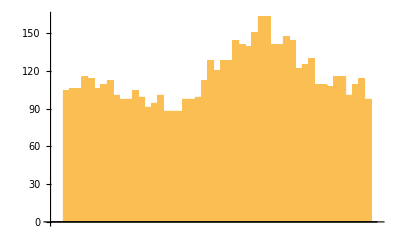

```mathematica
BarChart[ToExpression/@smallList]
```